# Eulerian Graph Q function

## Undirected graphs

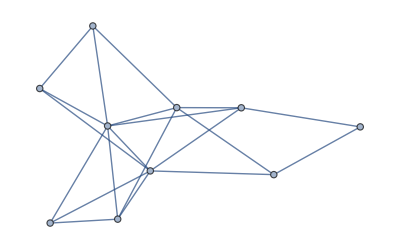

```mathematica
RandomGraph[{10,20}]
```

```mathematica
EulerianGraphQ[RandomGraph[{10,20}]]
```

False

## Directed Graphs

```mathematica
RandomGraph[{10,20},DirectedEdges->True]
```

-Graphics-

```mathematica
EulerianGraphQ[RandomGraph[{10,20},DirectedEdges->True]]
```

False

## Mixed Graphs

### Even

```mathematica
EvenCondition[graph_?ConnectedGraphQ]:=AllTrue[VertexDegree[graph],EvenQ]
```

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

Get::noopen: Cannot open PeterBurbery`MixedGraphs`.

Needs::nocont: Context PeterBurbery`MixedGraphs` was not created when Needs was evaluated.

$Failed

```mathematica
PacletInstall[ResourceObject["PeterBurbery/MixedGraphs"]]
```

PacletObject[…]

## Even but not balanced

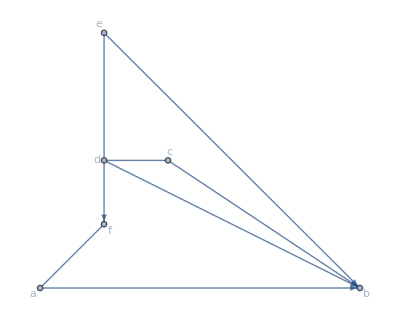

```mathematica
evenbutnotbalanced=Graph[{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b},VertexLabels->Automatic,GraphLayout->"PlanarEmbedding"]
```

```mathematica
EulerianGraphQ[evenbutnotbalanced]
```

EulerianGraphQ::ngen: The generalized EulerianGraphQ[Graph[<6>, <8>]] is not implemented.

EulerianGraphQ[-Graphics-]

```mathematica
EvenCondition[evenbutnotbalanced]
```

True

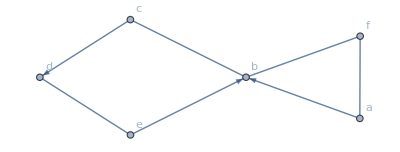

```mathematica
evenandbalanced=Graph[{a,b,c,d,e,f},{a->b,b<->c,c->d,d<->e,e->b,a<->f,f<->b},VertexLabels->Automatic]
```

```mathematica
EvenCondition[evenandbalanced]
```

True

## Balanced Set Condition

```mathematica
VertexList[evenandbalanced]
```

{a,b,c,d,e,f}

```mathematica
Subsets[VertexList[evenandbalanced]]
```

{{},{a},{b},{c},{d},{e},{f},{a,b},{a,c},{a,d},{a,e},{a,f},{b,c},{b,d},{b,e},{b,f},{c,d},{c,e},{c,f},{d,e},{d,f},{e,f},{a,b,c},{a,b,d},{a,b,e},{a,b,f},{a,c,d},{a,c,e},{a,c,f},{a,d,e},{a,d,f},{a,e,f},{b,c,d},{b,c,e},{b,c,f},{b,d,e},{b,d,f},{b,e,f},{c,d,e},{c,d,f},{c,e,f},{d,e,f},{a,b,c,d},{a,b,c,e},{a,b,c,f},{a,b,d,e},{a,b,d,f},{a,b,e,f},{a,c,d,e},{a,c,d,f},{a,c,e,f},{a,d,e,f},{b,c,d,e},{b,c,d,f},{b,c,e,f},{b,d,e,f},{c,d,e,f},{a,b,c,d,e},{a,b,c,d,f},{a,b,c,e,f},{a,b,d,e,f},{a,c,d,e,f},{b,c,d,e,f},{a,b,c,d,e,f}}

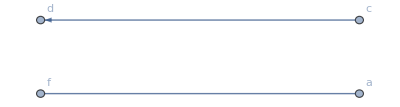

```mathematica
Subgraph[evenandbalanced,{a,c,d,f}]
```

```mathematica
evenandbalanced
```

-Graphics-

```mathematica
IncidenceList[evenandbalanced,Alternatives@@{a,c,d,f}]
```

{a->b,b<->c,c->d,d<->e,a<->f,f<->b}

```mathematica
EdgeCount[evenandbalanced,_->Alternatives@@{a,c,d,f}]
```

1

```mathematica
EdgeCount[evenandbalanced,Alternatives@@{a,c,d,f}->_]
```

2

```mathematica
AllTrue[Subsets[VertexList[evenandbalanced]],EdgeCount[evenandbalanced,_->Alternatives@@#]<=EdgeCount[evenandbalanced,Alternatives@@#->_]&]
```

False

```mathematica
?AllTrue
```

```mathematica
AllTrue[Subsets[VertexList[evenandbalanced]],EdgeCount[evenandbalanced,_->Alternatives@@#]>=EdgeCount[evenandbalanced,Alternatives@@#->_]&]
```

False

```mathematica
Select[!(EdgeCount[evenandbalanced,_->Alternatives@@#]<=EdgeCount[evenandbalanced,Alternatives@@#->_])&][Subsets[VertexList[evenandbalanced]]]
```

{{b},{d},{a,b},{b,c},{b,d},{b,e},{b,f},{d,f},{a,b,d},{a,b,f},{b,c,d},{b,c,f},{b,d,e},{b,d,f},{b,e,f},{a,b,c,d},{a,b,d,e},{a,b,d,f},{b,c,d,e},{b,c,d,f},{b,d,e,f},{a,b,c,d,f},{a,b,d,e,f},{b,c,d,e,f}}

```mathematica
EdgeCount[evenandbalanced,_->Alternatives@@#]<=EdgeCount[evenandbalanced,Alternatives@@#->_]&[{b,f}]
```

False

```mathematica
EdgeList[evenandbalanced,_->b|f]
```

{a->b,e->b}

```mathematica
EdgeList[evenandbalanced,b|f->_]
```

{}

```mathematica
AllTrue[Subsets[VertexList[evenbutnotbalanced]],EdgeCount[evenbutnotbalanced,_->Alternatives@@#]<=EdgeCount[evenbutnotbalanced,Alternatives@@#->_]&]
```

False

```mathematica
Table[{EdgeCount[evenbutnotbalanced,_->Alternatives@@k],EdgeCount[evenbutnotbalanced,Alternatives@@#->_]&[k],EdgeCount[evenbutnotbalanced,Alternatives@@k<->_]},{k,Subsets[VertexList[evenbutnotbalanced]]}]
```

{{0,0,0},{0,1,1},{3,0,1},{0,0,2},{0,2,2},{0,1,1},{1,0,1},{3,1,2},{0,1,3},{0,3,3},{0,2,2},{1,1,1},{3,0,2},{3,2,3},{3,1,2},{4,0,2},{0,2,3},{0,1,3},{1,0,3},{0,3,2},{1,2,3},{1,1,2},{3,1,3},{3,3,4},{3,2,3},{4,1,2},{0,3,4},{0,2,4},{1,1,3},{0,4,3},{1,3,3},{1,2,2},{3,2,3},{3,1,3},{4,0,3},{3,3,3},{4,2,4},{4,1,3},{0,3,3},{1,2,4},{1,1,4},{1,3,3},{3,3,4},{3,2,4},{4,1,3},{3,4,4},{4,3,4},{4,2,3},{0,4,4},{1,3,4},{1,2,4},{1,4,3},{3,3,3},{4,2,4},{4,1,4},{4,3,4},{1,3,4},{3,4,4},{4,3,4},{4,2,4},{4,4,4},{1,4,4},{4,3,4},{4,4,4}}